# R3M Multidimensional Timeline

## Visualizing Multi-Dimensional Evidence

-Graphics-

The purpose of analytical displays of information is to assist thinking about evidence:

What are the evidence-thinking tasks that this display is supposed to serve?

Analytical graphics should be constructed to serve the fundamental cognitive tasks in reasoning about evidence:

Describing the data

Making comparisons

Understanding causality

Assessing credibility of data and analysis

Logic of design replicates the logic of analysis and supports the narrative

Design reasoning emulates evidence reasoning

Spare design, content resolution. Simple designs, complex information"

-Graphics-

## Early Examples

-Graphics-

## One Dimensional Evidence

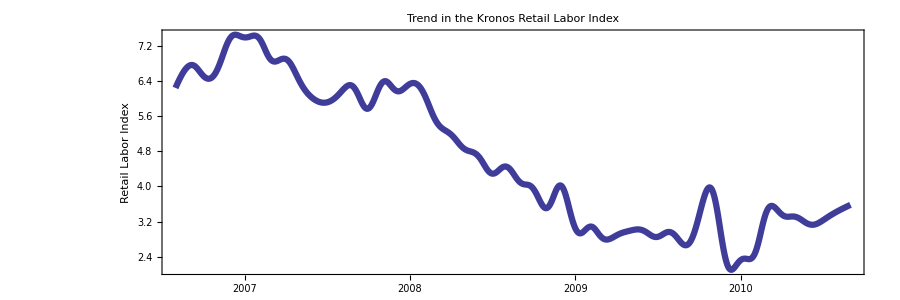

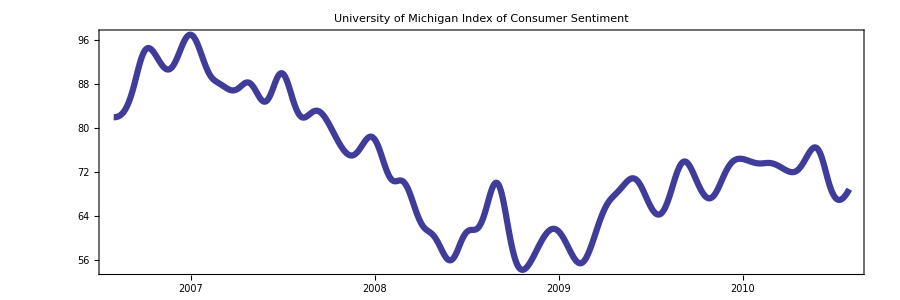

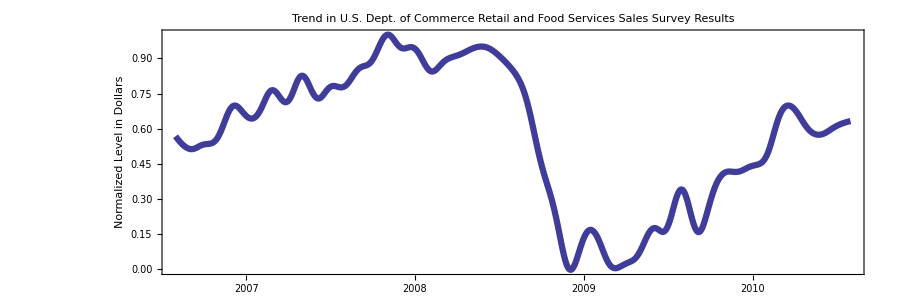

## Two Dimensions of Evidence

## Three Dimensions of Evidence

## R3M Visualization

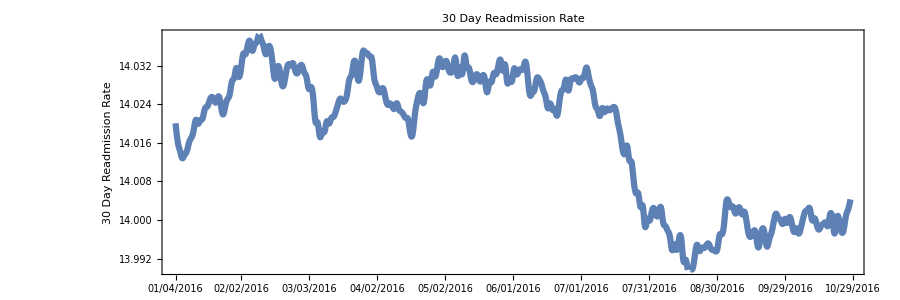

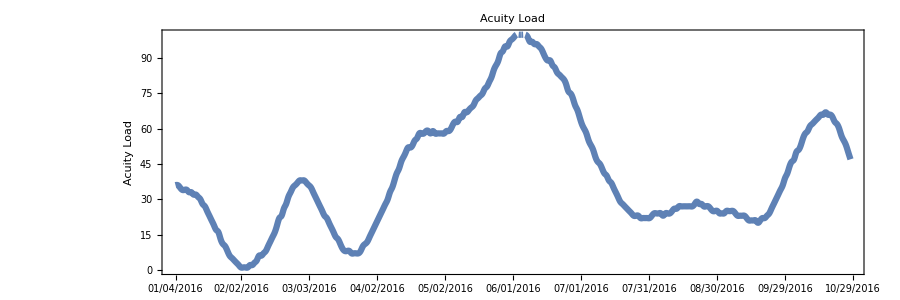

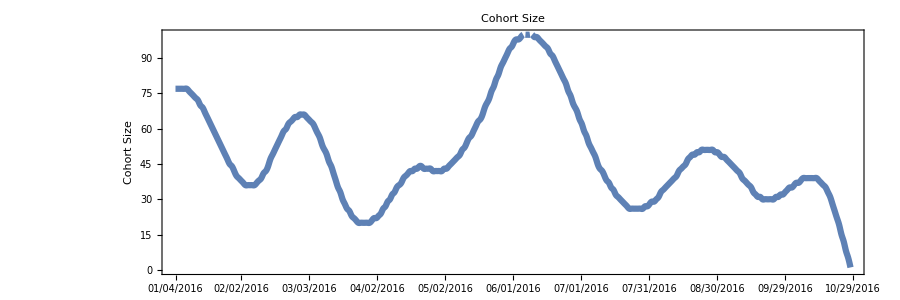

-Graphics-

```mathematica
Needs["PlotLegends`"]
lSmoothingRate = 1/40;
R3M = Import["C:\\Users\\ry5t\\Workspaces\\Neon1\\R3MVisuals\\DataSet_1.xlsx"][[2]];
dschrgDate = Transpose[R3M][[1,1;;300]];
dschrgCount = Transpose[R3M][[2,1;;300]];
admitCount = Transpose[R3M][[3,1;;300]];
readmitRate = Transpose[R3M][[4,1;;300]];
cohortCount = Transpose[R3M][[5,1;;300]];
cohortLoad = Transpose[R3M][[6,1;;300]];

ReadmitRateRelative = ExponentialMovingAverage[readmitRate, lSmoothingRate];
AcuityRate = cohortLoad;
CohortSizeRelative = cohortCount;

AcuityRateSmoothed = ExponentialMovingAverage[AcuityRate, lSmoothingRate];
AcuityRateScaled = Round[99*((AcuityRateSmoothed - Min[AcuityRateSmoothed])/(Max[AcuityRateSmoothed] - 
         	Min[AcuityRateSmoothed])) + 1];
      
CohortSizeSmoothed = ExponentialMovingAverage[CohortSizeRelative, lSmoothingRate];
CohortSizeScaled = Round[99*(( CohortSizeSmoothed - Min[ CohortSizeSmoothed])/(Max[ CohortSizeSmoothed] - Min[ CohortSizeSmoothed])) + 1]; 

(* AcuityRateTemp is a color scale I designed by blending over a range of 300 gradations *)
Temp1 = Table[{Blend[{Black, Gray}, x]}, {x, 0, 1, 1/10}];
Temp2 = Table[{Blend[{Gray, Orange}, x]}, {x, 0, 1, 1/52}];
Temp3 = Table[{Blend[{Orange, Red}, x]}, {x, 0, 1, 1/38}];
AcuityRateTemp = Join[Temp1,Temp2,Temp3];

(*  colorAcuityRate is a function that is passed to the Mathematica graphing engine and allows me to 
	dynamically change the color of the plot based on the value of a variable that is not on the x or y axes  
	The built in Mathematica color variation function such as what is seen in 3-D surface plots assumes that the
	color is set based on the value of x,y, or z. *)


ColorAcuityRate = Function[{x, y},AcuityRateTemp[[AcuityRateScaled[[Round[x+1]]]]]];

(*  I also need to create my own Legend as the Graphics Engine has no idea what I'm doing  ! I create my own legend 
    by building a small graphic that is essentially a horizontal bar-graph. The color with the bar transitions at 
    a constant rate across the full scale of values used in the graph. *)

ColorAcuityRateLegend = Function[{x, y}, AcuityRateTemp[[x]]];

AcuityRateLegend = ListLinePlot[ConstantArray[0.1, 100], ColorFunction -> ColorAcuityRateLegend, 
   	ColorFunctionScaling -> False, Frame -> True, Axes -> {False, False}, 
   	FrameTicks -> {{None, None}, {{{1, Round[Min[AcuityRate], 0.1]}, 
       		{50, Round[Min[AcuityRate] + (Max[AcuityRate] - Min[AcuityRate])/2, 0.1]}, 
       		{300, Round[Max[AcuityRate], 0.1]}}, None}}, 
       FrameLabel -> {Style["Acuity Load", 14, Bold], None}, 
   	PlotStyle -> Directive[Thickness[1]], ImageSize -> 300, AspectRatio -> 1/15];
   	
   	
WidthRange=.08;
MinWidth=.04;
lPlotStyle = PlotStyle->Directive[Thickness[.005],JoinForm["Round"]];
lFrameLabel=FrameLabel->{Style["","AxesTitle"],Style["30 Day Readmission Rate","AxesTitle"]};
lPlotLabel=PlotLabel-> Style["30 Day Readmission Rate"];
lFrameTicks =FrameTicks->{{Automatic,None},{{{0,"01/04/2016"},{29,"02/02/2016"},{59,"03/03/2016"},{89,"04/02/2016"},
											{119,"05/02/2016"},{149,"06/01/2016"},{179,"07/01/2016"},{209,"07/31/2016"},
											{239,"08/30/2016"},{269,"09/29/2016"},{299,"10/29/2016"}},None}};
DateListPlot[{ReadmitRateRelative},{0,298},InterpolationOrder->3,Joined -> True,lFrameLabel,lFrameTicks,lPlotLabel, 
Axes->{False,False}, lPlotStyle,ImageSize->900,AspectRatio->1/3]
lPlotStyle = PlotStyle->Directive[Thickness[.005],JoinForm["Round"]];
lFrameLabel=FrameLabel->{Style["","AxesTitle"],Style["Acuity Load","AxesTitle"]};
lPlotLabel=PlotLabel-> Style["Acuity Load"];
DateListPlot[{AcuityRateScaled},{0,298},InterpolationOrder->3,Joined -> True,lFrameLabel,lFrameTicks,lPlotLabel, 
Axes->{False,False}, lPlotStyle,ImageSize->900,AspectRatio->1/3]
lPlotStyle = PlotStyle->Directive[Thickness[.005],JoinForm["Round"]];
lFrameLabel=FrameLabel->{Style["","AxesTitle"],Style["Cohort Size","AxesTitle"]};
lPlotLabel=PlotLabel-> Style["Cohort Size"];
DateListPlot[{CohortSizeScaled},{0,298},InterpolationOrder->3,Joined -> True,lFrameLabel,lFrameTicks,lPlotLabel, 
Axes->{False,False}, lPlotStyle,ImageSize->900,AspectRatio->1/3]
WidthRange=.08;
MinWidth=.04;
ReadmitRateRelativeRange=Max[ReadmitRateRelative]-Min[ReadmitRateRelative];
ReadmitRateRelativeU=Take[ReadmitRateRelative[[]],298]+((MinWidth*ReadmitRateRelativeRange)+((Take[CohortSizeScaled[[]],298]/300)*(WidthRange*ReadmitRateRelativeRange)));
ReadmitRateRelativeL=Take[ReadmitRateRelative[[]],298]-((MinWidth*ReadmitRateRelativeRange)+((Take[CohortSizeScaled[[]],298]/300)*(WidthRange*ReadmitRateRelativeRange)));
lPlotStyle = PlotStyle->Directive[Thickness[.0001],JoinForm["Round"]];
lFrameLabel=FrameLabel->{Style["","AxesTitle"],Style["30 Day Readmission Rate","AxesTitle"]};
lPlotLabel=PlotLabel-> Style["30 Day Readmission Rate, Cohort Size, Patient Acuity"];
lFrameTicks =FrameTicks->{{Automatic,None},{{{0,"01/04/2016"},{29,"02/02/2016"},{59,"03/03/2016"},{89,"04/02/2016"},{119,"05/02/2016"},{149,"06/01/2016"},{179,"07/01/2016"},{209,"07/31/2016"},{239,"08/30/2016"},{269,"09/29/2016"},{299,"10/29/2016"}},None}};
lColorFunction = ColorFunction->ColorAcuityRate;
lEpilog=Epilog->Inset[ AcuityRateLegend ,Offset[{-750,-270},Scaled[{1,1}]],{Left,Bottom}];
DateListPlot[{ReadmitRateRelativeU,ReadmitRateRelativeL},{0,298},InterpolationOrder->3,Filling->{1->{2}},Joined -> True,lFrameLabel,lFrameTicks,lPlotLabel, 
Axes->{False,False}, lColorFunction,ColorFunctionScaling->False,lPlotStyle,ImageSize->900,lEpilog,AspectRatio->1/3]
```